## First formulae

```mathematica
MpgChain2[g_,glayout_:"TutteEmbedding",previous_:{}, positions_:Null,size_:{}, highlight_:{}]:=Block[{contract, result, coord, newPos=positions,newSize=size, layout, thegraph,form,graphs,first,newNeighbors},
If[VertexCount[g]==4,Return[{}]];
Table[
contract=EdgeContract[g,e];
If[MaximalPlanarQ[contract],
If[positions==Null,
layout = Graph[
SortGraph[g],
GraphLayout->glayout,
GraphHighlightStyle->"Thick",
ImageSize->{6 cm,6 cm}, 
VertexCoordinates->Automatic
];
newPos=First[AbsoluteOptions[layout, VertexCoordinates]][[2]];
newSize=First[AbsoluteOptions[layout, ImageSize]][[2]];
];
coord=newPos;(*Table[newPos[[k]],{k,VertexList[g]}];*)
form=FindFullFormula4[g];
newNeighbors=Intersection[VertexList[NeighborhoodGraph[g,e[[1]]]],VertexList[NeighborhoodGraph[g,e[[2]]]]];
If[form≠{},first=First[form];form=SymbolToColoring[first]];
thegraph=Graph[
Range[Length[newPos]],
EdgeList[g],
GraphHighlightStyle->"Thick",
VertexLabels->Map[If[MemberQ[highlight,#[[1]]],#[[1]]->Style[#[[2]],Directive[Red,Underlined]],#]&,Map[If[MemberQ[newNeighbors,#],#->Framed[#],If[MemberQ[previous,#],#->ToString[previous],#->#]]&,VertexList[g]]],
GraphHighlight->Select[CollectMPGEdges[g],#=!=e&],
VertexLabelStyle->Directive[Darker[Green],Italic,10],
ImageSize->newSize, 
AspectRatio->1,
EdgeStyle->{e->{Thick,Blue,Dashed}}, 
VertexStyle->form, 
VertexSize->Map[#->If[MemberQ[previous,#],Larger[Large],Large]&,VertexList[g]],
VertexCoordinates->coord
];
result=Prepend[MpgChain2[contract,glayout,{e[[1]],e[[2]]}, newPos,newSize,newNeighbors],{Labeled[
thegraph,{Style[ChromaticPolynomial[g,4]/24,Green ],e,Grid[Transpose[Map[{#,VertexDegree[g,#]}&,Sort[VertexList[g]]]],Frame->All]}],
FormatAdjacencyMatrix[g,VertexList[NeighborhoodGraph[VertexContract[ thegraph,e],e[[1]]]]],
FormatAdjacencyMatrix[VertexAdd[VertexContract[ g,e],e[[2]]],VertexList[NeighborhoodGraph[VertexContract[ thegraph,e],e[[1]]]]],
Labeled[SolGraph[g,first,newNeighbors, highlight],highlight],
graphs=Table[
With[{sub=NeighborhoodGraph[ thegraph,v]},
Graph[EdgeList[sub],VertexSize->Medium,GraphLayout->"SpringElectricalEmbedding",VertexStyle->Select[form,MemberQ[VertexList[sub],#[[1]]]&],VertexLabels->"Name",EdgeStyle->{e->{Thick,Blue,Dashed}},ImageSize->{3 cm,3 cm}]
],
{v,{e[[1]],e[[2]]}}
];
With[
{sub=GraphUnion[graphs[[1]],graphs[[2]]]},
Labeled[Graph[EdgeList[sub],VertexSize->Large,GraphLayout->"PlanarEmbedding",VertexStyle->Select[form,MemberQ[VertexList[sub],#[[1]]]&],VertexLabels->"Name",EdgeStyle->{e->{Thick,Blue,Dashed}},ImageSize->{4 cm,4 cm}],e]]

}];
Goto[stop]
]
,{e,EdgeList[g]}
];
Label[stop];
result
]
```

## Then experiments

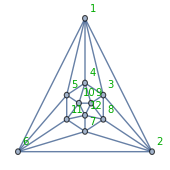
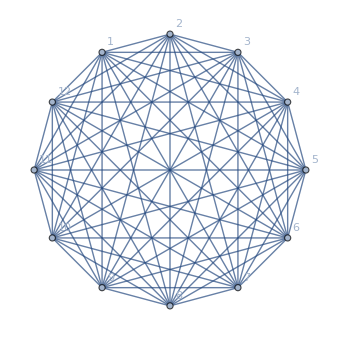
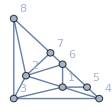
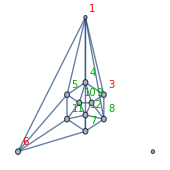
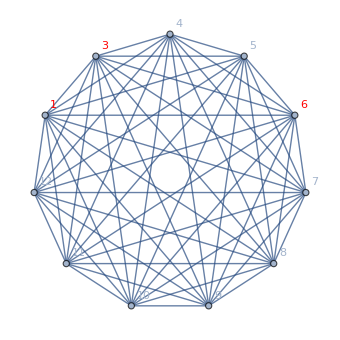
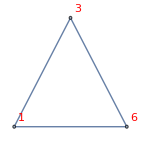
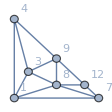
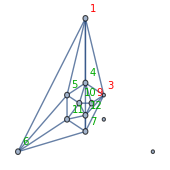
{{-Graphics-{10,1<->2,1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5},( | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
1 | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
2 | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
3 | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ●
4 | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ●
5 | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ●
6 | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ●
7 | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ●
8 | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ●
9 | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ●
10 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ●
11 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ●
12 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆),( | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
1 | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
2 | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
3 | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ●
4 | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ●
5 | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ●
6 | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ●
7 | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ●
8 | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ●
9 | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ●
10 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ●
11 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ●
12 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆),{-Graphics-,-Graphics-}vertices:12, non-edges:36, taken:12, not-taken:24{},-Graphics-1<->2},{-Graphics-{8,3<->8,1 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
6 | 4 | 5 | 5 | 4 | 5 | 5 | 5 | 5 | 5 | 5},( | 1 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
1 | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
3 | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ●
4 | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ●
5 | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ●
6 | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ●
7 | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ●
8 | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ●
9 | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ●
10 | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ●
11 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ●
12 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆),( | 1 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
1 | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
3 | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ●
4 | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ●
5 | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ●
6 | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ●
7 | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ●
8 | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ●
9 | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ●
10 | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ●
11 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ●
12 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆),{-Graphics-,-Graphics-}vertices:11, non-edges:28, taken:10, not-taken:18{1,2,3,6},-Graphics-3<->8},{-Graphics-{8,4<->9,1 | 3 | 4 | 5 | 6 | 7 | 9 | 10 | 11 | 12
5 | 5 | 5 | 5 | 4 | 5 | 4 | 5 | 5 | 5},( | 1 | 3 | 4 | 5 | 6 | 7 | 9 | 10 | 11 | 12
1 | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ●
3 | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ●
4 | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ●
5 | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ●
6 | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ●
7 | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ●
9 | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ●
10 | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ●
11 | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ●
12 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆),( | 1 | 3 | 4 | 5 | 6 | 7 | 9 | 10 | 11 | 12
1 | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ●
3 | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ●
4 | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ●
5 | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ●
6 | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ●
7 | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ●
9 | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ●
10 | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ●
11 | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ●
12 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆),{-Graphics-,-Graphics-}vertices:10, non-edges:21, taken:8, not-taken:13{1,3,8,9},-Graphics-4<->9},{-Graphics-{2,5<->10,1 | 3 | 4 | 5 | 6 | 7 | 10 | 11 | 12
5 | 4 | 5 | 5 | 4 | 5 | 4 | 5 | 5},( | 1 | 3 | 4 | 5 | 6 | 7 | 10 | 11 | 12
1 | ◆ | ● | ● | ● | ● | ● | ● | ● | ●
3 | ● | ◆ | ● | ● | ● | ● | ● | ● | ●
4 | ● | ● | ◆ | ● | ● | ● | ● | ● | ●
5 | ● | ● | ● | ◆ | ● | ● | ● | ● | ●
6 | ● | ● | ● | ● | ◆ | ● | ● | ● | ●
7 | ● | ● | ● | ● | ● | ◆ | ● | ● | ●
10 | ● | ● | ● | ● | ● | ● | ◆ | ● | ●
11 | ● | ● | ● | ● | ● | ● | ● | ◆ | ●
12 | ● | ● | ● | ● | ● | ● | ● | ● | ◆),( | 1 | 3 | 4 | 5 | 6 | 7 | 10 | 11 | 12
1 | ◆ | ● | ● | ● | ● | ● | ● | ● | ●
3 | ● | ◆ | ● | ● | ● | ● | ● | ● | ●
4 | ● | ● | ◆ | ● | ● | ● | ● | ● | ●
5 | ● | ● | ● | ◆ | ● | ● | ● | ● | ●
6 | ● | ● | ● | ● | ◆ | ● | ● | ● | ●
7 | ● | ● | ● | ● | ● | ◆ | ● | ● | ●
10 | ● | ● | ● | ● | ● | ● | ◆ | ● | ●
11 | ● | ● | ● | ● | ● | ● | ● | ◆ | ●
12 | ● | ● | ● | ● | ● | ● | ● | ● | ◆),{-Graphics-,-Graphics-}vertices:9, non-edges:15, taken:6, not-taken:9{3,4,9,10},-Graphics-5<->10},{-Graphics-{3,6<->11,1 | 3 | 4 | 5 | 6 | 7 | 11 | 12
5 | 4 | 4 | 5 | 4 | 5 | 4 | 5},( | 1 | 3 | 4 | 5 | 6 | 7 | 11 | 12
1 | ◆ | ● | ● | ● | ● | ● | ● | ●
3 | ● | ◆ | ● | ● | ● | ● | ● | ●
4 | ● | ● | ◆ | ● | ● | ● | ● | ●
5 | ● | ● | ● | ◆ | ● | ● | ● | ●
6 | ● | ● | ● | ● | ◆ | ● | ● | ●
7 | ● | ● | ● | ● | ● | ◆ | ● | ●
11 | ● | ● | ● | ● | ● | ● | ◆ | ●
12 | ● | ● | ● | ● | ● | ● | ● | ◆),( | 1 | 3 | 4 | 5 | 6 | 7 | 11 | 12
1 | ◆ | ● | ● | ● | ● | ● | ● | ●
3 | ● | ◆ | ● | ● | ● | ● | ● | ●
4 | ● | ● | ◆ | ● | ● | ● | ● | ●
5 | ● | ● | ● | ◆ | ● | ● | ● | ●
6 | ● | ● | ● | ● | ◆ | ● | ● | ●
7 | ● | ● | ● | ● | ● | ◆ | ● | ●
11 | ● | ● | ● | ● | ● | ● | ◆ | ●
12 | ● | ● | ● | ● | ● | ● | ● | ◆),{-Graphics-,-Graphics-}vertices:8, non-edges:10, taken:4, not-taken:6{4,5,10,11},-Graphics-6<->11},{-Graphics-{5,7<->12,1 | 3 | 4 | 5 | 6 | 7 | 12
5 | 4 | 4 | 4 | 4 | 4 | 5},( | 1 | 3 | 4 | 5 | 6 | 7 | 12
1 | ◆ | ● | ● | ● | ● | ● | ●
3 | ● | ◆ | ● | ● | ● | ● | ●
4 | ● | ● | ◆ | ● | ● | ● | ●
5 | ● | ● | ● | ◆ | ● | ● | ●
6 | ● | ● | ● | ● | ◆ | ● | ●
7 | ● | ● | ● | ● | ● | ◆ | ●
12 | ● | ● | ● | ● | ● | ● | ◆),( | 1 | 3 | 4 | 5 | 6 | 7 | 12
1 | ◆ | ● | ● | ● | ● | ● | ●
3 | ● | ◆ | ● | ● | ● | ● | ●
4 | ● | ● | ◆ | ● | ● | ● | ●
5 | ● | ● | ● | ◆ | ● | ● | ●
6 | ● | ● | ● | ● | ◆ | ● | ●
7 | ● | ● | ● | ● | ● | ◆ | ●
12 | ● | ● | ● | ● | ● | ● | ◆),{-Graphics-,-Graphics-}vertices:7, non-edges:6, taken:3, not-taken:3{5,6,7,11},-Graphics-7<->12},{-Graphics-{1,3<->1,1 | 3 | 4 | 5 | 6 | 7
5 | 3 | 4 | 4 | 3 | 5},( | 1 | 3 | 4 | 5 | 6 | 7
1 | ◆ | ● | ● | ● | ● | ●
3 | ● | ◆ | ● | ● | ● | ●
4 | ● | ● | ◆ | ● | ● | ●
5 | ● | ● | ● | ◆ | ● | ●
6 | ● | ● | ● | ● | ◆ | ●
7 | ● | ● | ● | ● | ● | ◆),( | 1 | 3 | 4 | 5 | 6 | 7
1 | ◆ | ● | ● | ● | ● | ●
3 | ● | ◆ | ● | ● | ● | ●
4 | ● | ● | ◆ | ● | ● | ●
5 | ● | ● | ● | ◆ | ● | ●
6 | ● | ● | ● | ● | ◆ | ●
7 | ● | ● | ● | ● | ● | ◆),{-Graphics-,-Graphics-}vertices:6, non-edges:3, taken:2, not-taken:1{3,6,7,12},-Graphics-3<->1},{-Graphics-{1,5<->4,1 | 4 | 5 | 6 | 7
4 | 3 | 4 | 3 | 4},( | 1 | 4 | 5 | 6 | 7
1 | ◆ | ● | ● | ● | ●
4 | ● | ◆ | ● | ● | ●
5 | ● | ● | ◆ | ● | ●
6 | ● | ● | ● | ◆ | ●
7 | ● | ● | ● | ● | ◆),( | 1 | 4 | 5 | 6 | 7
1 | ◆ | ● | ● | ● | ●
4 | ● | ◆ | ● | ● | ●
5 | ● | ● | ◆ | ● | ●
6 | ● | ● | ● | ◆ | ●
7 | ● | ● | ● | ● | ◆),{-Graphics-,-Graphics-}vertices:5, non-edges:1, taken:1, not-taken:0{1,3,4,7},-Graphics-5<->4}}

```mathematica
MpgChain2[Graph[plantri [[1]] ] ]
```